# もうひとつのページランク -Hitsアルゴリズム-

webページに対し、”ハブ”と”オーソリティ”のふたつの評価を行う(Google PageRankはひとつ)

ハブとして評価されるページは、たくさんの(他のページへの)リンクを持つページ

オーソリティとして評価されるページは、たくさんの(他のページからの)バックリンクを持つページ

## Nav: top

## 計算の流れ:

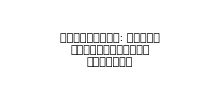
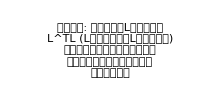
-Graphics-
 | I | II | III | IV | V | VI
I | 0 | 0 | 1 | 0 | 1 | 0
II | 1 | 0 | 0 | 0 | 0 | 0
III | 0 | 0 | 0 | 0 | 1 | 0
IV | 0 | 0 | 0 | 0 | 0 | 0
V | 0 | 0 | 1 | 1 | 0 | 0
VI | 0 | 0 | 0 | 0 | 1 | 0
-Graphics- | -Graphics- |  | I | II | III | IV | V | VI
I | 1 | 0 | 0 | 0 | 0 | 0
II | 0 | 0 | 0 | 0 | 0 | 0
III | 0 | 0 | 2 | 1 | 1 | 0
IV | 0 | 0 | 1 | 1 | 0 | 0
V | 0 | 0 | 1 | 0 | 3 | 0
VI | 0 | 0 | 0 | 0 | 0 | 0
-Graphics- | -Graphics- |  | I | II | III | IV | V | VI
I | 0.958 | 0.008 | 0.008 | 0.008 | 0.008 | 0.008
II | 0.008 | 0.008 | 0.008 | 0.008 | 0.008 | 0.008
III | 0.008 | 0.008 | 1.908 | 0.958 | 0.958 | 0.008
IV | 0.008 | 0.008 | 0.958 | 0.958 | 0.008 | 0.008
V | 0.008 | 0.008 | 0.958 | 0.008 | 2.858 | 0.008
VI | 0.008 | 0.008 | 0.008 | 0.008 | 0.008 | 0.008
-Graphics-
-Graphics-
I | II | III | IV | V | VI
0.0032 | 0.0023 | 0.3634 | 0.1351 | 0.4936 | 0.0023
 |  |  |  | 
 | -Graphics- |  | I | II | III | IV | V | VI
I | 2 | 0 | 1 | 0 | 1 | 1
II | 0 | 1 | 0 | 0 | 0 | 0
III | 1 | 0 | 1 | 0 | 0 | 1
IV | 0 | 0 | 0 | 0 | 0 | 0
V | 1 | 0 | 0 | 0 | 2 | 0
VI | 1 | 0 | 1 | 0 | 0 | 1
-Graphics- | -Graphics- |  | I | II | III | IV | V | VI
I | 1.908 | 0.008 | 0.958 | 0.008 | 0.958 | 0.958
II | 0.008 | 0.958 | 0.008 | 0.008 | 0.008 | 0.008
III | 0.958 | 0.008 | 0.958 | 0.008 | 0.008 | 0.958
IV | 0.008 | 0.008 | 0.008 | 0.008 | 0.008 | 0.008
V | 0.958 | 0.008 | 0.008 | 0.008 | 1.908 | 0.008
VI | 0.958 | 0.008 | 0.958 | 0.008 | 0.008 | 0.958
-Graphics-
-Graphics-
I | II | III | IV | V | VI
0.3628 | 0.0032 | 0.2106 | 0.0023 | 0.2106 | 0.2106

## PageRankとの計算上の違い:

ベクトルが規格化されていない

## See also

Google PageRank

以上webコンテンツ

## Programs

### google page soce

```mathematica
toAdjacency[t_]:=Map[If[#>0,1,0]&,t,{2}]
```

```mathematica
ellipseLayout[n_,{a_,b_}]:=Table[{a Cos[2Pi/n u],b Sin[2Pi/n u]},{u,1,n}]
```

```mathematica
zeroSelf[mat_]:=Module[
{len,rl},
len=Length[mat];
rl=Table[{n,n}->0,{n,len}];
ReplacePart[mat,rl]
]
```

```mathematica
nextscore[{mat_,r_}]:={mat,Map[Tr,Transpose[(mat r)]]}
```

```mathematica
linkMatToH[mat_]:=Block[
{links},
links=Map[Tr,mat];
mat/links/.{Indeterminate->0}
]
```

```mathematica
hToG[mat_,alpha_]:=Block[
{n,zerolines,a,elem},
n=Length[mat];
zerolines=Position[Map[Tr,mat],0];
a=ReplacePart[Table[0,{n}],zerolines->1];
elem=Table[1,{n}];
mat*alpha+(alpha*a+(1-alpha)elem)*1/n
(*Transpose[Transpose[mat]*alpha+(alpha*a+(1-alpha)elem)*1/n]*)
]
```

```mathematica
googlePageScore[linkmat_,alpha_,itr_]:=Block[
{n,rstart,h,g},
n=Length[linkmat];
rstart=Table[1/n,{n}];
h=linkMatToH[linkmat];
g=hToG[h,alpha];
Nest[nextscore,{g,rstart},itr]
]
```

### Hits

```mathematica
StoG[m_,a_]:=m*a+(1-a)/Length[m]
```

### Eigen factor

```mathematica
hToE[mat_,alpha_,w_]:=Block[
{n,zerolines,a,elem},
n=Length[mat];
zerolines=Position[Map[Tr,mat],0];
a=ReplacePart[Table[0,{n}],zerolines->1];
(*elem=Table[1,{n}];*)
elem=w/Tr[w]*n;
Transpose[Transpose[mat]*alpha+(alpha*a+(1-alpha)elem)*1/n]
]
```

```mathematica
eigenPageScore[linkmat_,alpha_,w_,itr_]:=Block[
{n,rstart,h,g},
n=Length[linkmat];
rstart=Table[1/n,{n}];
h=linkMatToH[linkmat];
g=hToE[h,alpha,w];
Nest[nextscore,{g,rstart},itr]
]
```

## HITS基本

158ページ

L

```mathematica
l={{0,0,1,0,1,0},
{1,0,0,0,0,0},
{0,0,0,0,1,0},
{0,0,0,0,0,0},
{0,0,1,1,0,0},
{0,0,0,0,1,0}
}
```

{{0,0,1,0,1,0},{1,0,0,0,0,0},{0,0,0,0,1,0},{0,0,0,0,0,0},{0,0,1,1,0,0},{0,0,0,0,1,0}}

LLT

```mathematica
llT=l.Transpose[l]
```

{{2,0,1,0,1,1},{0,1,0,0,0,0},{1,0,1,0,0,1},{0,0,0,0,0,0},{1,0,0,0,2,0},{1,0,1,0,0,1}}

LTL

```mathematica
lTl=Transpose[l].l
```

{{1,0,0,0,0,0},{0,0,0,0,0,0},{0,0,2,1,1,0},{0,0,1,1,0,0},{0,0,1,0,3,0},{0,0,0,0,0,0}}

```mathematica
preAscore=Eigensystem[lTl][[2]][[1]]
```

{0,0,-1+√3,2-√3,1,0}

```mathematica
preHscore=Eigensystem[llT][[2]][[1]]
```

{√3,0,1,0,1,1}

xT (権威得点)

```mathematica
preAscore/Tr[preAscore]//N
```

{0.,0.,0.366025,0.133975,0.5,0.}

yT (ハブ得点)

```mathematica
preHscore/Tr[preHscore]//N
```

{0.366025,0.,0.211325,0.,0.211325,0.211325}

159ページ

```mathematica
lTl
```

{{1,0,0,0,0,0},{0,0,0,0,0,0},{0,0,2,1,1,0},{0,0,1,1,0,0},{0,0,1,0,3,0},{0,0,0,0,0,0}}

```mathematica
StoG[lTl,0.95]
```

{{0.958333,0.00833333,0.00833333,0.00833333,0.00833333,0.00833333},{0.00833333,0.00833333,0.00833333,0.00833333,0.00833333,0.00833333},{0.00833333,0.00833333,1.90833,0.958333,0.958333,0.00833333},{0.00833333,0.00833333,0.958333,0.958333,0.00833333,0.00833333},{0.00833333,0.00833333,0.958333,0.00833333,2.85833,0.00833333},{0.00833333,0.00833333,0.00833333,0.00833333,0.00833333,0.00833333}}

```mathematica
Map[Tr[#]&,Transpose[StoG[lTl,0.95]]]
```

{1.,0.05,3.85,1.95,3.85,0.05}

xT (ξ=0.95のときの権威得点)

```mathematica
prePAscore=Eigensystem[StoG[lTl,0.95]][[2]][[1]]
```

{-0.00507436,-0.00372267,-0.579005,-0.215309,-0.786347,-0.00372267}

```mathematica
xT=prePAscore/Tr[prePAscore]
```

{0.00318505,0.00233663,0.363427,0.135144,0.49357,0.00233663}

yT (ξ=0.95のときのハブ得点)

```mathematica
prePHscore=Eigensystem[StoG[llT,0.95]][[2]][[1]]
```

{-0.705299,-0.00616667,-0.409265,-0.00452877,-0.409265,-0.409265}

```mathematica
yT=prePHscore/Tr[prePHscore]
```

{0.362847,0.0031725,0.21055,0.00232987,0.21055,0.21055}

## コンテンツ作成

```mathematica
l={{0,0,1,0,1,0},
{1,0,0,0,0,0},
{0,0,0,0,1,0},
{0,0,0,0,0,0},
{0,0,1,1,0,0},
{0,0,0,0,1,0}
}
```

{{0,0,1,0,1,0},{1,0,0,0,0,0},{0,0,0,0,1,0},{0,0,0,0,0,0},{0,0,1,1,0,0},{0,0,0,0,1,0}}

```mathematica
vnames["l"]=Table[IntegerString[n,"Roman"],{n,Length[l]}]
```

{I,II,III,IV,V,VI}

```mathematica
vlabels["l"]=Table[n->Text[Style[IntegerString[n,"Roman"],Large]],{n,Length[l]}]
```

{1→I,2→II,3→III,4→IV,5→V,6→VI}

```mathematica
(*(l=ReplacePart[Table[RandomChoice[{1,0,0,0,0}],{8},{8}],Table[{n,n}->0,{n,8}]])//TableForm*)
```

以下は隣接行列からのグラフ表示です。

### スライド0

```mathematica
titleText[0]=Graphics[{FontSize->14,Text[Style["左上: ランダムサーファーモデル
導入直後の引用被引用ネット
ワーク

左下: その結合行列

下: 点数の初期値",TextAlignment->Left]]},ImageSize->{220,200}];
```

#### 初期状態

```mathematica
regend["m"]=Graphics[{FontSize->14,Text[Style["初期状態の隣接行列: 行で見ると
リンク、列で見るとバック
リンクである。
",TextAlignment->Left]]},ImageSize->{220,100}];
```

```mathematica
tb["m"]=TableForm[l,TableHeadings->{vnames["l"],vnames["l"]},TableSpacing->{1,2}]
```

| I | II | III | IV | V | VI
I | 0 | 0 | 1 | 0 | 1 | 0
II | 1 | 0 | 0 | 0 | 0 | 0
III | 0 | 0 | 0 | 0 | 1 | 0
IV | 0 | 0 | 0 | 0 | 0 | 0
V | 0 | 0 | 1 | 1 | 0 | 0
VI | 0 | 0 | 0 | 0 | 1 | 0

```mathematica
gr["m"]=AdjacencyGraph[l,VertexCoordinates->ellipseLayout[6,{1.4,1}],VertexLabels->vlabels["l"],ImagePadding->{{7,40},{0,30}},ImageSize->{220,160}]
```

-Graphics-

```mathematica
tbset["m"]=TableForm[{gr["m"],tb["m"],regend[0,0]}]
```

-Graphics-
 | I | II | III | IV | V | VI
I | 0 | 0 | 1 | 0 | 1 | 0
II | 1 | 0 | 0 | 0 | 0 | 0
III | 0 | 0 | 0 | 0 | 1 | 0
IV | 0 | 0 | 0 | 0 | 0 | 0
V | 0 | 0 | 1 | 1 | 0 | 0
VI | 0 | 0 | 0 | 0 | 1 | 0
-Graphics-

#### Arrow

```mathematica
arrow[1,1]=Graphics[{Arrowheads[0.2],Arrow[{{0,0},{2,3}}]},ImageSize->{50,75}]
```

-Graphics-

```mathematica
arrow[1,2]=Graphics[{Arrowheads[0.2],Arrow[{{0,0},{2,-3}}]},ImageSize->{50,75}]
```

-Graphics-

#### 権威行列

```mathematica
lTl
```

{{1,0,0,0,0,0},{0,0,0,0,0,0},{0,0,2,1,1,0},{0,0,1,1,0,0},{0,0,1,0,3,0},{0,0,0,0,0,0}}

```mathematica
regend["lTl"]=Graphics[{FontSize->12,Text[Style["権威行列: 隣接行列をLとすると、
L^TL (Lの転置行列とLとの行列積)
で算出される。バックリンクを
リンクで重み付けしたものと
考えてよい。",TextAlignment->Left,LineSpacing->{0.3,10}]]},ImageSize->{220,100}];
```

```mathematica
tb["lTl"]=TableForm[lTl,TableHeadings->{vnames["l"],vnames["l"]},TableSpacing->{1,2}]
```

| I | II | III | IV | V | VI
I | 1 | 0 | 0 | 0 | 0 | 0
II | 0 | 0 | 0 | 0 | 0 | 0
III | 0 | 0 | 2 | 1 | 1 | 0
IV | 0 | 0 | 1 | 1 | 0 | 0
V | 0 | 0 | 1 | 0 | 3 | 0
VI | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
tbset["lTl"]=TableForm[{tb["lTl"],regend["lTl"]}]
```

| I | II | III | IV | V | VI
I | 1 | 0 | 0 | 0 | 0 | 0
II | 0 | 0 | 0 | 0 | 0 | 0
III | 0 | 0 | 2 | 1 | 1 | 0
IV | 0 | 0 | 1 | 1 | 0 | 0
V | 0 | 0 | 1 | 0 | 3 | 0
VI | 0 | 0 | 0 | 0 | 0 | 0
-Graphics-

#### ハブ行列

```mathematica
llT
```

{{2,0,1,0,1,1},{0,1,0,0,0,0},{1,0,1,0,0,1},{0,0,0,0,0,0},{1,0,0,0,2,0},{1,0,1,0,0,1}}

```mathematica
regend["llT"]=Graphics[{FontSize->12,Text[Style["ハブ行列: 隣接行列をLとすると、
LL^T (LとLの転置行列との行列積)
で算出される。リンクをバックリンク
で重み付けしたものと考えてよい。",TextAlignment->Left,LineSpacing->{0.3,10}]]},ImageSize->{220,80}];
```

```mathematica
tb["llT"]=TableForm[llT,TableHeadings->{vnames["l"],vnames["l"]},TableSpacing->{1,2}]
```

| I | II | III | IV | V | VI
I | 2 | 0 | 1 | 0 | 1 | 1
II | 0 | 1 | 0 | 0 | 0 | 0
III | 1 | 0 | 1 | 0 | 0 | 1
IV | 0 | 0 | 0 | 0 | 0 | 0
V | 1 | 0 | 0 | 0 | 2 | 0
VI | 1 | 0 | 1 | 0 | 0 | 1

```mathematica
tbset["llT"]=TableForm[{tb["llT"],regend["llT"]}]
```

| I | II | III | IV | V | VI
I | 2 | 0 | 1 | 0 | 1 | 1
II | 0 | 1 | 0 | 0 | 0 | 0
III | 1 | 0 | 1 | 0 | 0 | 1
IV | 0 | 0 | 0 | 0 | 0 | 0
V | 1 | 0 | 0 | 0 | 2 | 0
VI | 1 | 0 | 1 | 0 | 0 | 1
-Graphics-

#### Arrow

```mathematica
arrow[3,1]=Graphics[{Arrowheads[0.3],Arrow[{{0,0},{2,0}}]},ImageSize->{30,200}]
```

-Graphics-

```mathematica
arrow[3,2]=Graphics[{Arrowheads[0.3],Arrow[{{0,0},{2,0}}]},ImageSize->{30,200}]
```

-Graphics-

#### 権威行列+テレポーテーション行列

```mathematica
tb["lTl","G"]=TableForm[Round[StoG[lTl,0.95],0.001],TableHeadings->{vnames["l"],vnames["l"]},TableSpacing->{1,1.1}]
```

| I | II | III | IV | V | VI
I | 0.958 | 0.008 | 0.008 | 0.008 | 0.008 | 0.008
II | 0.008 | 0.008 | 0.008 | 0.008 | 0.008 | 0.008
III | 0.008 | 0.008 | 1.908 | 0.958 | 0.958 | 0.008
IV | 0.008 | 0.008 | 0.958 | 0.958 | 0.008 | 0.008
V | 0.008 | 0.008 | 0.958 | 0.008 | 2.858 | 0.008
VI | 0.008 | 0.008 | 0.008 | 0.008 | 0.008 | 0.008

```mathematica
Round[lTl*0.95+0.05/6,0.001]//TableForm
```

0.958 | 0.008 | 0.008 | 0.008 | 0.008 | 0.008
0.008 | 0.008 | 0.008 | 0.008 | 0.008 | 0.008
0.008 | 0.008 | 1.908 | 0.958 | 0.958 | 0.008
0.008 | 0.008 | 0.958 | 0.958 | 0.008 | 0.008
0.008 | 0.008 | 0.958 | 0.008 | 2.858 | 0.008
0.008 | 0.008 | 0.008 | 0.008 | 0.008 | 0.008

```mathematica
regend["lTl","G"]=Graphics[{FontSize->12,Text[Style["修正された権威行列: 権威行列全体に定数(ここでは
0.95)を掛け、さらにその行列全体に(1-0.95)/n
を足す。これに対しPageRankと同様にスコアを
もとめると権威得点となる。",TextAlignment->Left,LineSpacing->{0.3,10}]]},ImageSize->{310,80}];
```

```mathematica
arrow[4,1]=Graphics[{Arrowheads[0.5],Arrow[{{0,0},{0,-2}}]},ImageSize->{300,20}]
```

-Graphics-

```mathematica
tb["xT"]=TableForm[{Round[xT,0.0001]},TableHeadings->{None,vnames["l"]},TableSpacing->{1,1.1}]
```

I | II | III | IV | V | VI
0.0032 | 0.0023 | 0.3634 | 0.1351 | 0.4936 | 0.0023

```mathematica
tbset["lTl","G"]=TableForm[{tb["lTl","G"],regend["lTl","G"],arrow[4,1],tb["xT"]}]
```

| I | II | III | IV | V | VI
I | 0.958 | 0.008 | 0.008 | 0.008 | 0.008 | 0.008
II | 0.008 | 0.008 | 0.008 | 0.008 | 0.008 | 0.008
III | 0.008 | 0.008 | 1.908 | 0.958 | 0.958 | 0.008
IV | 0.008 | 0.008 | 0.958 | 0.958 | 0.008 | 0.008
V | 0.008 | 0.008 | 0.958 | 0.008 | 2.858 | 0.008
VI | 0.008 | 0.008 | 0.008 | 0.008 | 0.008 | 0.008
-Graphics-
-Graphics-
I | II | III | IV | V | VI
0.0032 | 0.0023 | 0.3634 | 0.1351 | 0.4936 | 0.0023

#### ハブ行列+テレポーテーション行列

```mathematica
tb["llT","G"]=TableForm[Round[StoG[llT,0.95],0.001],TableHeadings->{vnames["l"],vnames["l"]},TableSpacing->{1,1.1}]
```

| I | II | III | IV | V | VI
I | 1.908 | 0.008 | 0.958 | 0.008 | 0.958 | 0.958
II | 0.008 | 0.958 | 0.008 | 0.008 | 0.008 | 0.008
III | 0.958 | 0.008 | 0.958 | 0.008 | 0.008 | 0.958
IV | 0.008 | 0.008 | 0.008 | 0.008 | 0.008 | 0.008
V | 0.958 | 0.008 | 0.008 | 0.008 | 1.908 | 0.008
VI | 0.958 | 0.008 | 0.958 | 0.008 | 0.008 | 0.958

```mathematica
Round[llT*0.95+0.05/6,0.001]//TableForm
```

1.908 | 0.008 | 0.958 | 0.008 | 0.958 | 0.958
0.008 | 0.958 | 0.008 | 0.008 | 0.008 | 0.008
0.958 | 0.008 | 0.958 | 0.008 | 0.008 | 0.958
0.008 | 0.008 | 0.008 | 0.008 | 0.008 | 0.008
0.958 | 0.008 | 0.008 | 0.008 | 1.908 | 0.008
0.958 | 0.008 | 0.958 | 0.008 | 0.008 | 0.958

```mathematica
regend["llT","G"]=Graphics[{FontSize->12,Text[Style["修正されたハブ行列: ハブ行列全体に定数(ここでは
0.95)を掛け、さらにその行列全体に(1-0.95)/n
を足す。これに対しPageRankと同様にスコアを
もとめるとハブ得点となる。",TextAlignment->Left,LineSpacing->{0.3,10}]]},ImageSize->{310,80}];
```

```mathematica
arrow[4,2]=Graphics[{Arrowheads[0.5],Arrow[{{0,0},{0,-2}}]},ImageSize->{300,20}]
```

-Graphics-

```mathematica
tb["yT"]=TableForm[{Round[yT,0.0001]},TableHeadings->{None,vnames["l"]},TableSpacing->{1,1.1}]
```

I | II | III | IV | V | VI
0.3628 | 0.0032 | 0.2106 | 0.0023 | 0.2106 | 0.2106

```mathematica
tbset["llT","G"]=TableForm[{tb["llT","G"],regend["llT","G"],arrow[4,2],tb["yT"]}]
```

| I | II | III | IV | V | VI
I | 1.908 | 0.008 | 0.958 | 0.008 | 0.958 | 0.958
II | 0.008 | 0.958 | 0.008 | 0.008 | 0.008 | 0.008
III | 0.958 | 0.008 | 0.958 | 0.008 | 0.008 | 0.958
IV | 0.008 | 0.008 | 0.008 | 0.008 | 0.008 | 0.008
V | 0.958 | 0.008 | 0.008 | 0.008 | 1.908 | 0.008
VI | 0.958 | 0.008 | 0.958 | 0.008 | 0.008 | 0.958
-Graphics-
-Graphics-
I | II | III | IV | V | VI
0.3628 | 0.0032 | 0.2106 | 0.0023 | 0.2106 | 0.2106

### スライド0

```mathematica
slide[0]=Grid[
{
{tbset["m"],arrow[1,1],tbset["lTl"],arrow[3,1],tbset["lTl","G"]},
{SpanFromAbove,Null,Null,Null,Null},
{SpanFromAbove,arrow[1,2],tbset["llT"],arrow[3,2],tbset["llT","G"]}
},(*Frame->All,*)
Alignment->{{Left,Right,Right,Right,Right},{Center,Center}}]
```

-Graphics-
 | I | II | III | IV | V | VI
I | 0 | 0 | 1 | 0 | 1 | 0
II | 1 | 0 | 0 | 0 | 0 | 0
III | 0 | 0 | 0 | 0 | 1 | 0
IV | 0 | 0 | 0 | 0 | 0 | 0
V | 0 | 0 | 1 | 1 | 0 | 0
VI | 0 | 0 | 0 | 0 | 1 | 0
-Graphics- | -Graphics- |  | I | II | III | IV | V | VI
I | 1 | 0 | 0 | 0 | 0 | 0
II | 0 | 0 | 0 | 0 | 0 | 0
III | 0 | 0 | 2 | 1 | 1 | 0
IV | 0 | 0 | 1 | 1 | 0 | 0
V | 0 | 0 | 1 | 0 | 3 | 0
VI | 0 | 0 | 0 | 0 | 0 | 0
-Graphics- | -Graphics- |  | I | II | III | IV | V | VI
I | 0.958 | 0.008 | 0.008 | 0.008 | 0.008 | 0.008
II | 0.008 | 0.008 | 0.008 | 0.008 | 0.008 | 0.008
III | 0.008 | 0.008 | 1.908 | 0.958 | 0.958 | 0.008
IV | 0.008 | 0.008 | 0.958 | 0.958 | 0.008 | 0.008
V | 0.008 | 0.008 | 0.958 | 0.008 | 2.858 | 0.008
VI | 0.008 | 0.008 | 0.008 | 0.008 | 0.008 | 0.008
-Graphics-
-Graphics-
I | II | III | IV | V | VI
0.0032 | 0.0023 | 0.3634 | 0.1351 | 0.4936 | 0.0023
 |  |  |  | 
 | -Graphics- |  | I | II | III | IV | V | VI
I | 2 | 0 | 1 | 0 | 1 | 1
II | 0 | 1 | 0 | 0 | 0 | 0
III | 1 | 0 | 1 | 0 | 0 | 1
IV | 0 | 0 | 0 | 0 | 0 | 0
V | 1 | 0 | 0 | 0 | 2 | 0
VI | 1 | 0 | 1 | 0 | 0 | 1
-Graphics- | -Graphics- |  | I | II | III | IV | V | VI
I | 1.908 | 0.008 | 0.958 | 0.008 | 0.958 | 0.958
II | 0.008 | 0.958 | 0.008 | 0.008 | 0.008 | 0.008
III | 0.958 | 0.008 | 0.958 | 0.008 | 0.008 | 0.958
IV | 0.008 | 0.008 | 0.008 | 0.008 | 0.008 | 0.008
V | 0.958 | 0.008 | 0.008 | 0.008 | 1.908 | 0.008
VI | 0.958 | 0.008 | 0.958 | 0.008 | 0.008 | 0.958
-Graphics-
-Graphics-
I | II | III | IV | V | VI
0.3628 | 0.0032 | 0.2106 | 0.0023 | 0.2106 | 0.2106

## 作業メモおよび確認

スコアの算出

```mathematica
PGscore["c"]=Nest[nextScore[#,MtoG[c,0.9]]&,Table[1/numofnodes,{numofnodes}],40]
```

{0.317192,0.277365,0.0948946,0.310549}

```mathematica
Map[#/Tr[#]&,Eigensystem[Transpose[MtoG[c,0.9]]][[2]][[1]],{0}]
```

{0.317272,0.27731,0.0948726,0.310545}

収束していることの確認

```mathematica
PGscore["c"].MtoG[c,0.9]
```

{0.317331,0.277323,0.0948734,0.310472}

```mathematica
Map[Tr[#]&,MtoG[c,0.9]*PGscore["c"]]
```

{0.317192,0.277365,0.0948946,0.310549}

重みつき引用被引用行列

```mathematica
MtoG[c,0.9]*PGscore["c"]//TableForm
```

0.00792979 | 0.00792979 | 0.00792979 | 0.293402
0.256563 | 0.00693413 | 0.00693413 | 0.00693413
0.045075 | 0.045075 | 0.00237237 | 0.00237237
0.00776371 | 0.217384 | 0.0776371 | 0.00776371

```mathematica
{{a,b},{k,d}}*{e,f}
```

{{a e,b e},{f k,d f}}

```mathematica
gr[1]=AdjacencyGraph[toAdjacency[MtoG[c,0.9]],DirectedEdges->True,VertexLabels->vlabels[4],EdgeStyle->style[1],EdgeLabels->edgeforcelabels[1],ImagePadding->{{0,30},{0,30}},ImageSize->{400,220}]
```

-Graphics-